Expressions for constants of motion come from Celestial Mechanics in Kerr Spacetime (W. Schmidt)

```mathematica
<<KerrGeodesics`
SetOptions[$Output, PageWidth->Infinity];
```

```mathematica
ClearAll[e]
dechi = D[KerrGeoEnergy[χ,p,e,1], χ]//Simplify;
dep = D[KerrGeoEnergy[χ,p,e,1], p]//Simplify;
dlchi = D[KerrGeoAngularMomentum[χ,p,e,1],χ]//Simplify;
dlp = D[KerrGeoAngularMomentum[χ,p,e,1],p]//Simplify;


dpm =D[P/M,M]/.P->p*M;
dχm = D[J/M^2,M]/.J->χ*M^2;
```

```mathematica
res=M*D[KerrGeoEnergy[J*c/(G*M^2),P/(G*M/c^2),e,1],M]/.{J->χ*G*M^2/c,P->G*M*p/c^2}/.χ->a//Simplify;
Grid[{{Print["(∂E)/(∂M): "]},
{Print["Function of ",res//Variables]},
{res//FortranForm}
}]
```

(∂E)/(∂M):

Function of {a,e,p}

((1 - e**2)*(-1 + ((-1 + e**2)*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(4*a**2*(-1 + e**2)**2 - (3 + e**2 - p)**2*p) + ((-1 + e**2)*(16*a**2*(-1 + e**2)**2 - p*(e**4 + e**2*(6 - 4*p) + 3*(3 - 4*p + p**2)))*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)**2 + ((-1 + e**2)*(a**2*p + 4*a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)) + (-9*a**6*(-1 + e**2)**2 + a**2*p**2*(-12 + 12*e**2 + 16*p - 5*p**2) - 2*a**4*p*(-12 + 7*p + e**2*(12 + 7*p)) + p**4*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))/(p**2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)))/(2.*p*Sqrt(1 - ((1 - e**2)*(1 + ((-1 + e**2)*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)))/p))

```mathematica
res = M^2*D[KerrGeoEnergy[L/M^2,p,e,1],L]/.L->a*M^2//Simplify;
Grid[{{Print["(∂E)/(∂L): "]},
{Print["Function of ",res//Variables]},
{res//FortranForm}
}]
```

(∂E)/(∂L):

Function of {a,e,p}

-(((1 - e**2)*(-1 + e**2)*((-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)*(a*(1 + 3*e**2 + p) - (3*a**5*(-1 + e**2)**2 + a*(-4*e**2 + (-2 + p)**2)*p**2 + 4*a**3*p*(-2 + p + e**2*(2 + p)))/(p**2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))) + 4*a*(-1 + e**2)**2*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)))))/(p*(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)**2*Sqrt(1 - ((1 - e**2)*(1 + ((-1 + e**2)*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)))/p)))

```mathematica
res=M*D[KerrGeoAngularMomentum[J*c/(G*M^2),P/(G*M/c^2),e,1],M]/.{J->a*G*M^2/c,P->G*M*p/c^2}//Simplify;
Grid[{{Print["(∂L)/(∂M): "]},
{Print["Function of ",res//Variables]},
{res//FortranForm}
}]
```

(∂L)/(∂M):

Function of {a,e,p}

(-2*p*Sqrt((a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)) + (p*((-16*a**2*(-1 + e**2)**2 + p*(e**4 + e**2*(6 - 4*p) + 3*(3 - 4*p + p**2)))*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))) - (-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)*(a**2*p + 4*a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)) + (-9*a**6*(-1 + e**2)**2 + a**2*p**2*(-12 + 12*e**2 + 16*p - 5*p**2) - 2*a**4*p*(-12 + 7*p + e**2*(12 + 7*p)) + p**4*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))/(p**2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)))))/((-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)**2*Sqrt((a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p))) + (a*(1 - e**2)*(-1 + ((-1 + e**2)*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(4*a**2*(-1 + e**2)**2 - (3 + e**2 - p)**2*p) + ((-1 + e**2)*(16*a**2*(-1 + e**2)**2 - p*(e**4 + e**2*(6 - 4*p) + 3*(3 - 4*p + p**2)))*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)**2 + ((-1 + e**2)*(a**2*p + 4*a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)) + (-9*a**6*(-1 + e**2)**2 + a**2*p**2*(-12 + 12*e**2 + 16*p - 5*p**2) - 2*a**4*p*(-12 + 7*p + e**2*(12 + 7*p)) + p**4*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))/(p**2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)))/(p*Sqrt(1 - ((1 - e**2)*(1 + ((-1 + e**2)*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)))/p)) - 4*a*Sqrt(1 - ((1 - e**2)*(1 + ((-1 + e**2)*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)))/p))/2.

```mathematica
res = M^2*D[KerrGeoAngularMomentum[L/M^2,p,e,1],L]/.L->a*M^2//Simplify;
Grid[{{Print["(∂L)/(∂L): "]},
{Print["Function of ",res//Variables]},
{res//FortranForm}
}]
```

(∂L)/(∂L):

Function of {a,e,p}

(p*((-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)*(a*(1 + 3*e**2 + p) - (3*a**5*(-1 + e**2)**2 + a*(-4*e**2 + (-2 + p)**2)*p**2 + 4*a**3*p*(-2 + p + e**2*(2 + p)))/(p**2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))) + 4*a*(-1 + e**2)**2*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)))))/((-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)**2*Sqrt((a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p))) - (a*(1 - e**2)*(-1 + e**2)*((-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)*(a*(1 + 3*e**2 + p) - (3*a**5*(-1 + e**2)**2 + a*(-4*e**2 + (-2 + p)**2)*p**2 + 4*a**3*p*(-2 + p + e**2*(2 + p)))/(p**2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))) + 4*a*(-1 + e**2)**2*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3)))))/(p*(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)**2*Sqrt(1 - ((1 - e**2)*(1 + ((-1 + e**2)*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)))/p)) + Sqrt(1 - ((1 - e**2)*(1 + ((-1 + e**2)*(a**2*(1 + 3*e**2 + p) + p*(-3 - e**2 + p - 2*Sqrt((a**6*(-1 + e**2)**2 + a**2*(-4*e**2 + (-2 + p)**2)*p**2 + 2*a**4*p*(-2 + p + e**2*(2 + p)))/p**3))))/(-4*a**2*(-1 + e**2)**2 + (3 + e**2 - p)**2*p)))/p)

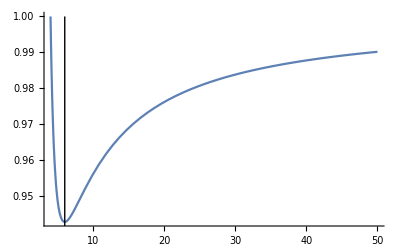

```mathematica
e=0.;
expr = FullSimplify[KerrGeoEnergy[0,p,e,1], Assumptions->p>3];
Plot[expr,{p,2,50}, PlotRange->{All,1}, Epilog->Line[{{6+2*e,0},{6+2*e,1}}]]//FullSimplify
```

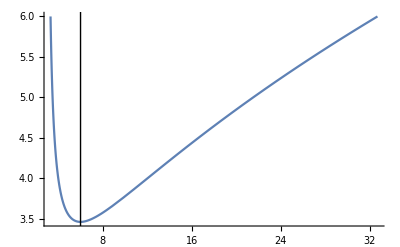

```mathematica
e=0.;
expr = FullSimplify[KerrGeoAngularMomentum[0,p,e,1], Assumptions->p>3];
Plot[expr,{p,2,50}, PlotRange->{All,6}, Epilog->Line[{{6+2*e,0},{6+2*e,10}}]]//FullSimplify
```